```mathematica
Mathematica Course
Sajad Aghapour, Danesh School
Session 01
```

Course Mathematica

### About Wolfram Alpha

```mathematica
TextCell["Hello, human."]
```

Hello, human.

WolframAlphaQueryParseResults

{{x→1/2 (-3-√37)},{x→1/2 (-3+√37)}}

```mathematica
(* Length Contraction *)
```

How to code more fluently/ using help/ comment

```mathematica
Solve[x^2+3 x -7 ==0, x] (* comment ... *)
```

{{x→1/2 (-3-√37)},{x→1/2 (-3+√37)}}

```mathematica
(* in x ke estefade shodel dakhel tabee Solve[], is a local variable, therefore, it is not saved as a defined variable. that is why it is still ib blue but not in black. *)
x^4 /. x->1/2 (-3-√37) // Expand
```

431/2+(69 √37)/2

#### Equal signs =, :=, ==, ===, and more ...

```mathematica
x = 2
```

2

```mathematica
Clear[x]
```

```mathematica
x = 3
```

3

```mathematica
? x
```

```mathematica
? Solve
```

```mathematica
f[x] = x^2
```

9

```mathematica
f[x] := x^2
```

```mathematica
g[x_ + y_] := (x+y)^2
```

```mathematica
g[3+4]
```

g[7]

```mathematica
g[a+b]
```

(a+b)^2

```mathematica
g[x_,y_] := (x+y)^3
```

```mathematica
? g
```

```mathematica
eq = x^3 + 8 == -10 (* an expression is assigned to an equation *)
```

False

```mathematica
False (* equal manteghi *)
```

False

```mathematica
eq2 = y^3+8 == -10
```

8+y^3==-10

```mathematica
eq2 /. y  -> 3
```

False

```mathematica
eq2
```

8+y^3==-10

```mathematica
Solve[eq2,y]
```

{{y→-(-3)^(2/3) 2^(1/3)},{y→(-2)^(1/3) 3^(2/3)},{y→-2^(1/3) 3^(2/3)}}

```mathematica
N[%] (* % yaani akharin chizi ke ejra shod*)
```

{{y→1.31037-2.26963 ⅈ},{y→1.31037+2.26963 ⅈ},{y→-2.62074}}

```mathematica
%% // N
```

{{y→1.31037-2.26963 ⅈ},{y→1.31037+2.26963 ⅈ},{y→-2.62074}}

```mathematica
N @ %%%
```

{{y→1.31037-2.26963 ⅈ},{y→1.31037+2.26963 ⅈ},{y→-2.62074}}

```mathematica
(* in se javab moadele ham ba se raveshe mokhtalef hastand *)
```

```mathematica
h[y_] := Sin[y] + y^2
```

```mathematica
D[h[y] , y]
```

2 y+Cos[y]

```mathematica
D[h[x],x]
```

General::ivar: 3 is not a valid variable.

∂_3 (9+Sin[3])

```mathematica
∂_3 (9+Sin[3]) (* aya moshtaghe 3rd mikhay begiri? *)
```

General::ivar: 3 is not a valid variable.

∂_3 (9+Sin[3])

```mathematica
D[h[z],z]
```

2 z+Cos[z]

```mathematica
Replace, ReplaceAll, Thread, Simplify, FullSimplify
```

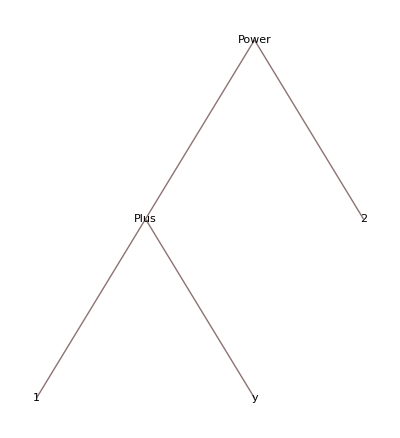

```mathematica
(1+y)^2 // TreeForm
```

```mathematica
Vectors and Matrices
```

and Matrices Vectors

```mathematica
? List
```

```mathematica
list1 = {a,b,3,Dina}
```

{a,b,3,Dina}

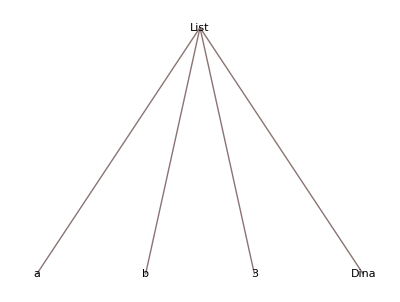

```mathematica
TreeForm[%]
```

```mathematica
list1[[2]]
```

b

```mathematica
Protect[b]
```

{b}

```mathematica
V = {x1, y1, z1};
```

```mathematica
W = {x2, y2, z2};
```

```mathematica
V.W
```

x1 x2+y1 y2+z1 z2

```mathematica
?Dot
```

```mathematica
Cross[V,W]
 % // MatrixForm
```

{-y2 z1+y1 z2,x2 z1-x1 z2,-x2 y1+x1 y2}

(-y2 z1+y1 z2
x2 z1-x1 z2
-x2 y1+x1 y2)

```mathematica
1/V
```

{1/x1,1/y1,1/z1}

```mathematica
V^2
```

{x1^2,y1^2,z1^2}

```mathematica
V.V
```

x1^2+y1^2+z1^2

```mathematica
R = {{Cos[θ], Sin[θ]} , {-Sin[θ], Cos[θ]}}
R // MatrixForm
```

{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}

(Cos[θ] | Sin[θ]
-Sin[θ] | Cos[θ])

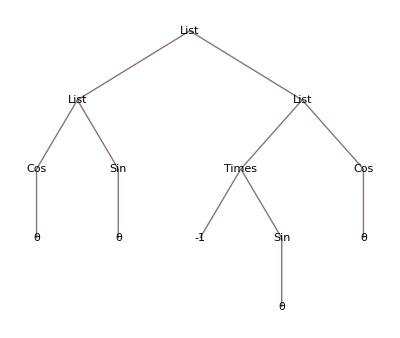

```mathematica
R // TreeForm
```

```mathematica
R[[2]]
```

{-Sin[θ],Cos[θ]}

```mathematica
R⟦2 ;;2⟧
```

{{-Sin[θ],Cos[θ]}}

```mathematica
? Part
```

```mathematica
ClearAll[x]
```

```mathematica
a = {x,y};
```

```mathematica
a -> R.a
```

{x,y}→{x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]}

```mathematica
(R.a).(R.a)
% // FullSimplify
```

(y Cos[θ]-x Sin[θ])^2+(x Cos[θ]+y Sin[θ])^2

x^2+y^2

```mathematica
a.a
```

x^2+y^2

```mathematica
(* help --> f1 *)
(* tutorials !! *)
```

```mathematica
Physics Example: SR
```

Physics (Example:SR)

one dimensional motion of a relativistic particle in a constant gravitational field
m = 1, c=1

```mathematica
eqMotion = D[x'[t]/(√(1-x'[t]^2)),t]==-g
```

(x'[t]^2 x''[t])/((1-x'[t]^2)^(3/2))+x''[t]/(√(1-x'[t]^2))==-g

```mathematica
v0rule = {v0^2-> 1-1/γ^2};
```

```mathematica
$Assumptions = { γ ∈ Reals, γ>1};
```

```mathematica
? DSolve
```

```mathematica
sol = (DSolve[{eqMotion, x[0]== x0, x'[0] == v0} , x[t], t] // FullSimplify) /. v0rule // FullSimplify
```

{{x[t]→(g x0+γ-√(g^2 t^2+2 g t v0 γ+γ^2))/g},{x[t]→(g x0-γ+√(g^2 t^2+2 g t v0 γ+γ^2))/g},{x[t]→(g x0+γ-√(g^2 t^2-2 g t v0 γ+γ^2))/g},{x[t]→(g x0-γ+√(g^2 t^2-2 g t v0 γ+γ^2))/g}}

```mathematica
(eqMotion /. x-> Function[t,x[t]/. sol] // FullSimplify) /. v0rule // Simplify // PowerExpand // Thread // Simplify
```

{True,g==0,True,g==0}

```mathematica
sol1 = x[t] /. sol ⟦1 ⟧
```

(g x0+γ-√(g^2 t^2+2 g t v0 γ+γ^2))/g

```mathematica
sol2 = x[t] /. sol⟦3⟧
```

(g x0+γ-√(g^2 t^2-2 g t v0 γ+γ^2))/g

```mathematica
Series[(sol1/.γ-> 1/(√(1-v0^2))), {g,0,1}, {v0,0,1}]
```

O[v0]^2/g+(x0-t v0+O[v0]^2)+(-t^2/2+O[v0]^2) g+O[g]^2

```mathematica
nonRelsol1 = Series[(sol1/.γ-> 1/(√(1-v0^2))), {g,0,1}, {v0,0,1}]// Normal
```

-(g t^2)/2-t v0+x0

```mathematica
nonRelsol2 = Series[(sol2/.γ-> 1/(√(1-v0^2))), {g,0,1}, {v0,0,1}]// Normal
```

-(g t^2)/2+t v0+x0

```mathematica
values = {x0->2, v0-> 2/3, g-> 0.1, γ-> 1/(√(1-v0^2))};
```

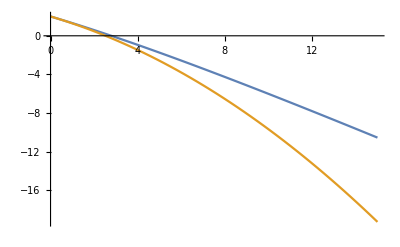

```mathematica
Plot[{sol1,nonRelsol1}//. values // Evaluate, {t, 0, 15}]
```

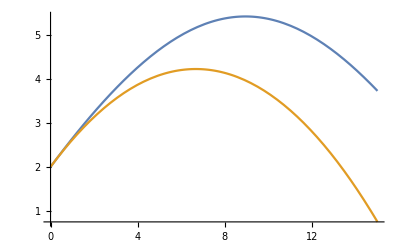

```mathematica
Plot[{sol2,nonRelsol2}//. values // Evaluate, {t, 0, 15}]
```

```mathematica
(* ReplaceRepeated --> //. evaluating a vector with a function *)
```